```mathematica
export[name_]:=Export["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>name<>".obj",ExampleData[{"Geometry3D",name}]]
```

```mathematica
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

```mathematica
ExampleData[{"Geometry3D","Cone"}]
```

-Graphics3D-

```mathematica
lineCount[model_]:=Module[
{polygons,lines},
polygons=ExampleData[{"Geometry3D",model},"PolygonData"];
lines=Union[Sort/@Flatten[Partition[#,2,1,1]&/@polygons,1]];
Length[lines]
]
```

```mathematica
{#,lineCount[#]}&/@ExampleData["Geometry3D"]⟦All,2⟧
```

{{BassGuitar,3600},{Beethoven,6090},{CastleWall,8177},{Cone,758},{Cow,8706},{Deimos,28224},{Galleon,6146},{HammerheadShark,5365},{Horse,14543},{KleinBottle,6101},{MoebiusStrip,528},{Phobos,28224},{PottedPlant,18548},{Seashell,2594},{SedanCar,15397},{SpaceShuttle,701},{StanfordBunny,104288},{Torus,13186},{Tree,32528},{Triceratops,5664},{Tugboat,72765},{UtahTeapot,928},{UtahVWBug,2277},{Vase,20403},{VikingLander,32155},{Wrench,6114},{Zeppelin,5083}}

```mathematica
lineCounts=%;
```

```mathematica
ClusteringComponents[SortBy[lineCounts,Last]⟦All,2⟧]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2}

```mathematica
export/@ExampleData["Geometry3D"]⟦All,2⟧
```

{E:\GDrive\GitHub\code\classes\cs546\pa2\objects\BassGuitar.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Beethoven.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\CastleWall.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Cone.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Cow.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Deimos.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Galleon.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\HammerheadShark.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Horse.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\KleinBottle.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\MoebiusStrip.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Phobos.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\PottedPlant.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Seashell.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\SedanCar.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\SpaceShuttle.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\StanfordBunny.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Torus.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Tree.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Triceratops.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Tugboat.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\UtahTeapot.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\UtahVWBug.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Vase.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\VikingLander.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Wrench.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Zeppelin.obj}

```mathematica
export["SedanCar"]
```

E:\GDrive\GitHub\code\classes\cs546\pa2\objects\StanfordBunny.obj

```mathematica
model="Horse";
vertices=Rescale[ExampleData[{"Geometry3D",model},"VertexData"]];
polygons=ExampleData[{"Geometry3D",model},"PolygonData"];
```

```mathematica
ExampleData[{"Geometry3D",model},"Properties"]
```

{Graphics3D,GraphicsComplex,Name,PolygonCount,PolygonData,PolygonObjects,VertexData,VertexNormals}

```mathematica
model="Horse";
```

```mathematica
size=500.0;
model="UtahTeapot";
vertices=size*Rescale[ExampleData[{"Geometry3D",model},"VertexData"]];
gc=ExampleData[{"Geometry3D",model},"GraphicsComplex"];
gc⟦1⟧=Rescale[vertices];
Export["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>model<>".obj",Graphics3D[gc]]
```

E:\GDrive\GitHub\code\classes\cs546\pa2\objects\UtahTeapot.obj

```mathematica
Graphics3D[gc,Axes->True]
```

-Graphics3D-

```mathematica
Import["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>model<>".obj"]
```

-Graphics3D-

```mathematica
{{rx1,rx2},{ry1,ry2},{rz1,rz2}}={Min[#],Max[#]}&/@Transpose[vertices]
```

{{67.3118,500.},{0.,269.247},{215.411,417.347}}

```mathematica
rx=rx2-rx1
ry=ry2-ry1
rz=rz2-rz1
```

432.688

269.247

201.936

```mathematica
rm=Max[rx,ry,rz]
```

432.688

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\UtahTeapot.obj",ExampleData[{"Geometry3D","UtahTeapot"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\UtahTeapot.obj

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\SpaceShuttle.obj",ExampleData[{"Geometry3D","SpaceShuttle"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\SpaceShuttle.obj

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\BassGuitar.obj",ExampleData[{"Geometry3D","BassGuitar"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\BassGuitar.obj

```mathematica
Union[Length/@polygons]
```

{3,4}

```mathematica
FullSimplify[RotationMatrix[tyz,{1,0,0}].(RotationMatrix[txz,{0,1,0}].(RotationMatrix[txy,{0,0,1}].{x,y,z})),Element[{tyz,txz,txy,x,y,z},Reals]]
```

{x Cos[txy] Cos[txz]-y Cos[txz] Sin[txy]+z Sin[txz],x Cos[tyz] Sin[txy]-(z Cos[txz]+y Sin[txy] Sin[txz]) Sin[tyz]+Cos[txy] (y Cos[tyz]+x Sin[txz] Sin[tyz]),z Cos[txz] Cos[tyz]+Cos[tyz] (-x Cos[txy]+y Sin[txy]) Sin[txz]+(y Cos[txy]+x Sin[txy]) Sin[tyz]}

```mathematica
exp=Expand@FullSimplify[{x Cos[txy] Cos[txz]-y Cos[txz] Sin[txy]+z Sin[txz],x Cos[tyz] Sin[txy]-(z Cos[txz]+y Sin[txy] Sin[txz]) Sin[tyz]+Cos[txy] (y Cos[tyz]+x Sin[txz] Sin[tyz]),z Cos[txz] Cos[tyz]+Cos[tyz] (-x Cos[txy]+y Sin[txy]) Sin[txz]+(y Cos[txy]+x Sin[txy]) Sin[tyz]}/.{x->x-size/2,y->y-size/2,z->z-size/2},Element[{size,ctyz,ctxz,ctxy,styz,stxz,stxy,x,y,z},Reals]]
```

{-1/2 size Cos[txy] Cos[txz]+x Cos[txy] Cos[txz]+1/2 size Cos[txz] Sin[txy]-y Cos[txz] Sin[txy]-1/2 size Sin[txz]+z Sin[txz],-1/2 size Cos[txy] Cos[tyz]+y Cos[txy] Cos[tyz]-1/2 size Cos[tyz] Sin[txy]+x Cos[tyz] Sin[txy]+1/2 size Cos[txz] Sin[tyz]-z Cos[txz] Sin[tyz]-1/2 size Cos[txy] Sin[txz] Sin[tyz]+x Cos[txy] Sin[txz] Sin[tyz]+1/2 size Sin[txy] Sin[txz] Sin[tyz]-y Sin[txy] Sin[txz] Sin[tyz],-1/2 size Cos[txz] Cos[tyz]+z Cos[txz] Cos[tyz]+1/2 size Cos[txy] Cos[tyz] Sin[txz]-x Cos[txy] Cos[tyz] Sin[txz]-1/2 size Cos[tyz] Sin[txy] Sin[txz]+y Cos[tyz] Sin[txy] Sin[txz]-1/2 size Cos[txy] Sin[tyz]+y Cos[txy] Sin[tyz]-1/2 size Sin[txy] Sin[tyz]+x Sin[txy] Sin[tyz]}

```mathematica
Depth[txy]
```

1

```mathematica
factorTerms[exp_]:=SortBy[Select[Tally[First[Last[Reap[Map[Sow,exp,Infinity]]]]],Depth[#⟦1⟧]>1&],-Last[#]&]
```

```mathematica
inReals[exp_]:=Element[Union[Cases[exp,_Symbol,Infinity]],Reals]
```

```mathematica
factorTerms[exp]
```

{{Cos[txy],10},{Cos[tyz],10},{Sin[txy],10},{Sin[txz],10},{Sin[tyz],10},{Cos[txz],8},{-1/2 size Cos[txy] Cos[txz],1},{x Cos[txy] Cos[txz],1},{-1/2 size Cos[txy] Cos[tyz],1},{y Cos[txy] Cos[tyz],1},{-1/2 size Cos[txz] Cos[tyz],1},{z Cos[txz] Cos[tyz],1},{1/2 size Cos[txz] Sin[txy],1},{-y Cos[txz] Sin[txy],1},{-1/2 size Cos[tyz] Sin[txy],1},{x Cos[tyz] Sin[txy],1},{-1/2 size Sin[txz],1},{z Sin[txz],1},{1/2 size Cos[txy] Cos[tyz] Sin[txz],1},{-x Cos[txy] Cos[tyz] Sin[txz],1},{-1/2 size Cos[tyz] Sin[txy] Sin[txz],1},{y Cos[tyz] Sin[txy] Sin[txz],1},{-1/2 size Cos[txy] Cos[txz]+x Cos[txy] Cos[txz]+1/2 size Cos[txz] Sin[txy]-y Cos[txz] Sin[txy]-1/2 size Sin[txz]+z Sin[txz],1},{-1/2 size Cos[txy] Sin[tyz],1},{y Cos[txy] Sin[tyz],1},{1/2 size Cos[txz] Sin[tyz],1},{-z Cos[txz] Sin[tyz],1},{-1/2 size Sin[txy] Sin[tyz],1},{x Sin[txy] Sin[tyz],1},{-1/2 size Cos[txy] Sin[txz] Sin[tyz],1},{x Cos[txy] Sin[txz] Sin[tyz],1},{1/2 size Sin[txy] Sin[txz] Sin[tyz],1},{-y Sin[txy] Sin[txz] Sin[tyz],1},{-1/2 size Cos[txz] Cos[tyz]+z Cos[txz] Cos[tyz]+1/2 size Cos[txy] Cos[tyz] Sin[txz]-x Cos[txy] Cos[tyz] Sin[txz]-1/2 size Cos[tyz] Sin[txy] Sin[txz]+y Cos[tyz] Sin[txy] Sin[txz]-1/2 size Cos[txy] Sin[tyz]+y Cos[txy] Sin[tyz]-1/2 size Sin[txy] Sin[tyz]+x Sin[txy] Sin[tyz],1},{-1/2 size Cos[txy] Cos[tyz]+y Cos[txy] Cos[tyz]-1/2 size Cos[tyz] Sin[txy]+x Cos[tyz] Sin[txy]+1/2 size Cos[txz] Sin[tyz]-z Cos[txz] Sin[tyz]-1/2 size Cos[txy] Sin[txz] Sin[tyz]+x Cos[txy] Sin[txz] Sin[tyz]+1/2 size Sin[txy] Sin[txz] Sin[tyz]-y Sin[txy] Sin[txz] Sin[tyz],1}}

```mathematica
exp2=FullSimplify[exp/.{
Cos[tyz]->ctyz,
Cos[txz]->ctxz,
Cos[txy]->ctxy,
Sin[tyz]->styz,
Sin[txz]->stxz,
Sin[txy]->stxy
},inReals[exp]]
```

{1/2 (-ctxy ctxz (size-2 x)+ctxz stxy (size-2 y)-stxz (size-2 z)),1/2 (-ctyz stxy (size-2 x)-ctxy (stxz styz (size-2 x)+ctyz (size-2 y))+styz (stxy stxz (size-2 y)+ctxz (size-2 z))),1/2 (-stxy (styz (size-2 x)+ctyz stxz (size-2 y))+ctxy (ctyz stxz (size-2 x)-styz (size-2 y))-ctxz ctyz (size-2 z))}

```mathematica
factorTerms[exp2]
```

{{size-2 x,5},{-2 x,5},{size-2 y,5},{-2 y,5},{size-2 z,3},{-2 z,3},{-ctxy ctxz (size-2 x),1},{-ctyz stxy (size-2 x),1},{ctyz stxz (size-2 x),1},{styz (size-2 x),1},{stxz styz (size-2 x),1},{stxz styz (size-2 x)+ctyz (size-2 y),1},{-ctxy (stxz styz (size-2 x)+ctyz (size-2 y)),1},{styz (size-2 x)+ctyz stxz (size-2 y),1},{-stxy (styz (size-2 x)+ctyz stxz (size-2 y)),1},{ctyz stxz (size-2 x)-styz (size-2 y),1},{ctxy (ctyz stxz (size-2 x)-styz (size-2 y)),1},{ctyz (size-2 y),1},{ctxz stxy (size-2 y),1},{ctyz stxz (size-2 y),1},{stxy stxz (size-2 y),1},{-styz (size-2 y),1},{1/2 (-ctyz stxy (size-2 x)-ctxy (stxz styz (size-2 x)+ctyz (size-2 y))+styz (stxy stxz (size-2 y)+ctxz (size-2 z))),1},{-ctyz stxy (size-2 x)-ctxy (stxz styz (size-2 x)+ctyz (size-2 y))+styz (stxy stxz (size-2 y)+ctxz (size-2 z)),1},{stxy stxz (size-2 y)+ctxz (size-2 z),1},{styz (stxy stxz (size-2 y)+ctxz (size-2 z)),1},{1/2 (-stxy (styz (size-2 x)+ctyz stxz (size-2 y))+ctxy (ctyz stxz (size-2 x)-styz (size-2 y))-ctxz ctyz (size-2 z)),1},{-stxy (styz (size-2 x)+ctyz stxz (size-2 y))+ctxy (ctyz stxz (size-2 x)-styz (size-2 y))-ctxz ctyz (size-2 z),1},{1/2 (-ctxy ctxz (size-2 x)+ctxz stxy (size-2 y)-stxz (size-2 z)),1},{-ctxy ctxz (size-2 x)+ctxz stxy (size-2 y)-stxz (size-2 z),1},{ctxz (size-2 z),1},{-ctxz ctyz (size-2 z),1},{-stxz (size-2 z),1}}

```mathematica
ClearAll[size]
```

```mathematica
exp3=FullSimplify[exp2/.{
(size-2 x)->s2x,
(size-2 y)->s2y,
(size-2 z)->s2z
},inReals[exp2]]
```

{1/2 (-ctxy ctxz s2x+ctxz s2y stxy-s2z stxz),1/2 (-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz)),-1/2 ctyz (ctxz s2z-ctxy s2x stxz+s2y stxy stxz)-1/2 (ctxy s2y+s2x stxy) styz}

```mathematica
exp4={
1/2 (-ctxy ctxz s2x+ctxz s2y stxy-s2z stxz)+size/2,
1/2 (-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz))+size/2,
-1/2 ctyz (ctxz s2z-ctxy s2x stxz+s2y stxy stxz)-1/2 (ctxy s2y+s2x stxy) styz+size/2
};
exp4=FullSimplify[exp4,inReals[exp4]]
```

{1/2 (-ctxy ctxz s2x+size+ctxz s2y stxy-s2z stxz),1/2 (size-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz)),1/2 (-ctxz ctyz s2z+size+ctyz (ctxy s2x-s2y stxy) stxz-(ctxy s2y+s2x stxy) styz)}

```mathematica
factorTerms[exp4]
```

{{ctxy s2x,1},{-ctxy ctxz s2x,1},{ctxy s2y,1},{ctyz s2y,1},{-ctxz ctyz s2z,1},{s2x stxy,1},{-ctyz s2x stxy,1},{-s2y stxy,1},{ctxz s2y stxy,1},{ctxy s2y+s2x stxy,1},{ctxy s2x-s2y stxy,1},{-s2z stxz,1},{ctyz (ctxy s2x-s2y stxy) stxz,1},{1/2 (-ctxy ctxz s2x+size+ctxz s2y stxy-s2z stxz),1},{-ctxy ctxz s2x+size+ctxz s2y stxy-s2z stxz,1},{ctxz s2z styz,1},{-(ctxy s2y+s2x stxy) styz,1},{s2x stxz styz,1},{s2y stxy stxz styz,1},{1/2 (-ctxz ctyz s2z+size+ctyz (ctxy s2x-s2y stxy) stxz-(ctxy s2y+s2x stxy) styz),1},{-ctxz ctyz s2z+size+ctyz (ctxy s2x-s2y stxy) stxz-(ctxy s2y+s2x stxy) styz,1},{ctyz s2y+s2x stxz styz,1},{-ctxy (ctyz s2y+s2x stxz styz),1},{1/2 (size-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz)),1},{size-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz),1}}

```mathematica
CForm[exp4⟦1⟧]
```

(-(ctxy*ctxz*s2x) + size + ctxz*s2y*stxy - s2z*stxz)/2.

```mathematica
CForm[exp4⟦2⟧]
```

(size - ctyz*s2x*stxy + ctxz*s2z*styz + s2y*stxy*stxz*styz - ctxy*(ctyz*s2y + s2x*stxz*styz))/2.

```mathematica
CForm[exp4⟦3⟧]
```

(-(ctxz*ctyz*s2z) + size + ctyz*(ctxy*s2x - s2y*stxy)*stxz - (ctxy*s2y + s2x*stxy)*styz)/2.

```mathematica
cases[term_]:=Cases[exp,term,Infinity]
```

```mathematica
cases[size/2]
```

{-size/2,-size/2}

```mathematica
FullSimplify[exp/.{
Cos[tyz]->ctyz,
Cos[txz]->ctxz,
Cos[txy]->ctxy,
Sin[tyz]->styz,
Sin[txz]->stxz,
Sin[txy]->stxy
},Element[{ctyz,ctxz,ctxy,styz,stxz,stxy,x,y,z},Reals]]
```

{ctxy ctxz x-ctxz stxy y+stxz z,ctyz stxy x+ctxy stxz styz x+ctxy ctyz y-stxy stxz styz y-ctxz styz z,-ctxy ctyz stxz x+stxy styz x+ctyz stxy stxz y+ctxy styz y+ctxz ctyz z}

```mathematica
CForm[%]
```

List(ctxy*ctxz*x - ctxz*stxy*y + stxz*z,ctyz*stxy*x + ctxy*stxz*styz*x + ctxy*ctyz*y - stxy*stxz*styz*y - 
    ctxz*styz*z,-(ctxy*ctyz*stxz*x) + stxy*styz*x + ctyz*stxy*stxz*y + ctxy*styz*y + ctxz*ctyz*z)

```mathematica
cases[Cos[tyz]]
cases[Cos[txz]]
cases[Cos[txy]]
```

{Cos[tyz],Cos[tyz],Cos[tyz],Cos[tyz]}

{Cos[txz],Cos[txz],Cos[txz],Cos[txz]}

{Cos[txy],Cos[txy],Cos[txy],Cos[txy]}

```mathematica
cases[Sin[txy]]
cases[Sin[txz]]
cases[Sin[txy]]
```

{Sin[txy],Sin[txy],Sin[txy],Sin[txy],Sin[txy]}

{Sin[txz],Sin[txz],Sin[txz],Sin[txz]}

{Sin[txy],Sin[txy],Sin[txy],Sin[txy],Sin[txy]}

```mathematica
cases[Cos[txz]]
```

{Cos[txz],Cos[txz],Cos[txz],Cos[txz]}

```mathematica
cases[Sin[txy]]
```

{Sin[txy],Sin[txy],Sin[txy],Sin[txy],Sin[txy]}

```mathematica
cases[Sin[txz]]
```

{Sin[txz],Sin[txz],Sin[txz],Sin[txz]}

```mathematica
%//CForm
```

List(x*Cos(txy)*Cos(txz) - y*Cos(txz)*Sin(txy) + z*Sin(txz),
   x*Cos(tyz)*Sin(txy) - (z*Cos(txz) + y*Sin(txy)*Sin(txz))*Sin(tyz) + 
    Cos(txy)*(y*Cos(tyz) + x*Sin(txz)*Sin(tyz)),
   z*Cos(txz)*Cos(tyz) + Cos(tyz)*(-(x*Cos(txy)) + y*Sin(txy))*Sin(txz) + (y*Cos(txy) + x*Sin(txy))*Sin(tyz))

```mathematica
{x Cos[t]-y Sin[t],y Cos[t]+x Sin[t],z}//CForm
```

List(x*Cos(t) - y*Sin(t),y*Cos(t) + x*Sin(t),z)

```mathematica
polygons=ExampleData[{"Geometry3D",model},"PolygonData"];
lines=Union[Sort/@Flatten[Partition[#,2,1,1]&/@polygons,1]];
```

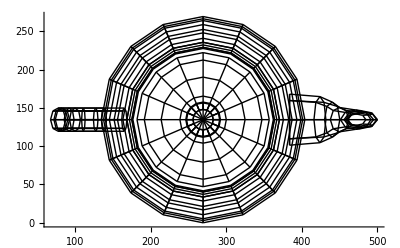

```mathematica
xy=Graphics[GraphicsComplex[vertices⟦All,{1,2}⟧,Line/@lines],Axes->True]
```

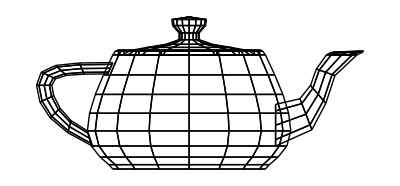

```mathematica
xz=Graphics[GraphicsComplex[vertices⟦All,{1,3}⟧,Line/@lines]]
```

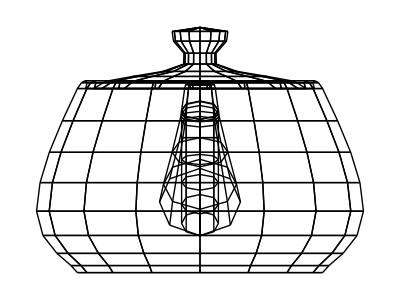

```mathematica
yz=Graphics[GraphicsComplex[vertices⟦All,{2,3}⟧,Line/@lines]]
```